```mathematica
(*FOR WHITE DWARF WITH CARBON*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=287.8*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_?NumericQ,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
mphi=10;
c=3*10^8;(*in m/s*)

g1[u_?NumericQ,mx_?NumericQ]:=(mphi^2*(1-1/βplus[mx]*u^2/(u^2+vesc^2)))/(mphi^2+mx^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

1.07143×10^-43

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= Min[1,δp[mx]/pf]*π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12,AccuracyGoal->5];
```

```mathematica
a[mx_?NumericQ,sigma_?NumericQ]:= Min[1,δp[mx]/pf]*π *R^2*Min[sigma/sigmaSat,1]*NIntegrate[g1[u,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,0,(vesc*βplus[mx]^0.5)/(1-βplus[mx])^0.5},MaxRecursion->12,AccuracyGoal->5];
```

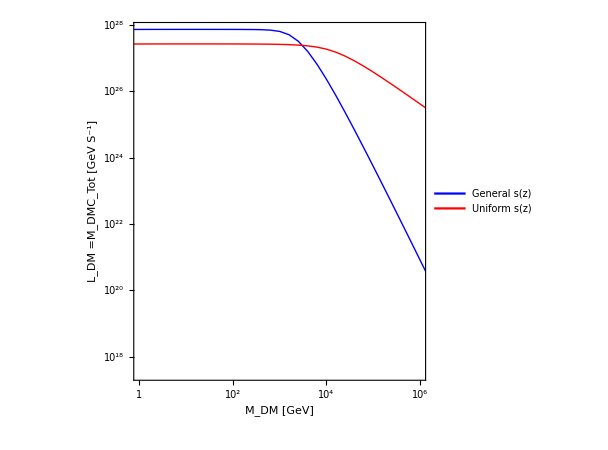

```mathematica
myticks={{{{10^28,"10^28"},{10^22,"10^22"},{10^16,"10^16"}},None},{{{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"}},None}};

ListLogPlot[{Table[{x,10^x*a[10^x,10^-43]},{x,-1,7,0.2}],Table[{x,10^x*CNNboosted[1,10^x,10^-43]},{x,-1,7,0.2}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->{{0,6},Automatic},Frame->True,FrameStyle->Directive[14, "Times",Black],PlotLegends->Placed[{Style["General s(z)",FontSize->20],Style["Uniform s(z)",FontSize->20]},{0.30,0.30}],AxesOrigin->{0,Automatic},FrameTicks->myticks,FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DMC_Tot [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450]
```

```mathematica
(*ROUGH*)
```

```mathematica
g1[u_]:=(mphi^2*(1-1/β*u^2/(u^2+vesc^2)))/(mphi^2+mx^2*1/β*(u/c)^2);
```

```mathematica
Solve[g1[u]==0,u]
```

{{u→-(vesc √β)/(√(1-β))},{u→(vesc √β)/(√(1-β))}}

```mathematica
Solve[g1[u]==1,u]
```

{{u→0},{u→0},{u→-(√(-c^2 mphi^2-mx^2 vesc^2))/mx},{u→(√(-c^2 mphi^2-mx^2 vesc^2))/mx}}

```mathematica
rlist=10^Subdivide[0,6,30];
lum={};
lumsingle={};
Do[
p=rlist[[i]];
AppendTo[lum,p*Ctotalnew[p,10^-43]];
AppendTo[lumsingle,p*CNNboosted[1,p,10^-43]];
,{i,Length[rlist]}]

Ldm=Table[{rlist[[i]]//N,lum[[i]]},{i,Length[rlist]}];
Ldmsingle=Table[{rlist[[i]]//N,lumsingle[[i]]},{i,Length[rlist]}];
Export["WD_Carbon_LTOT.csv",Ldm];
Export["WD_Carbon_Lsingle.csv",Ldmsingle];
```

```mathematica
ListLogLogPlot[Table[{rlist[[i]],lum[[i]]},{i,Length[rlist]}],PlotRange->All,Joined->True,PlotStyle->Blue,Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],ImageSize->450];
```

```mathematica
ListLogLogPlot[Table[{rlist[[i]],lumsingle[[i]]},{i,Length[rlist]}],PlotRange->All,Joined->True,PlotStyle->Red,Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],ImageSize->450];
```

```mathematica
(*FOR WHITE DWARF WITH NUCLEI*)
```

```mathematica
R=9*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mn *mx)/(mn+mx)^2;
```

```mathematica
umin[N_?NumericQ,mx_?NumericQ]:=vesc *√((1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
umax[N_?NumericQ,mx_?NumericQ]:=vesc *√(1/(1-βplus[mx])*(1/βplus[mx] Log[1/(1-βplus[mx])])^(N-1)-1);
```

```mathematica
gN[u_,N_?NumericQ,mx_?NumericQ]:=1/βplus[mx]*vesc^2/(vesc^2+u^2)*(1/βplus[mx]*Log[1/(1-βplus[mx])])^(N-1)-(1/βplus[mx]-1);
mphi=1;
c=3*10^8;(*in m/s*)

g1[u_?NumericQ,mx_?NumericQ]:=(mphi^2*(1-1/βplus[mx]*u^2/(u^2+vesc^2)))/(mphi^2+mx^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
Nn=4/3*π *R^3*n;
```

```mathematica
sigmaSat=(π *R^2)/Nn//N
```

8.33333×10^-44

```mathematica
tau[sigma_?NumericQ]:=Min[(3*sigma)/(2*sigmaSat),3/2];
```

```mathematica
pn[N_?NumericQ,sigma_?NumericQ]:=2/(Factorial[N]*tau[sigma]*tau[sigma])*(Gamma[N+2]-Gamma[(N+2),tau[sigma]]);
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
CNNboosted[N_?NumericQ,mx_?NumericQ,sigma_?NumericQ]:= π *R^2*pn[N,sigma]*NIntegrate[gN[u,N,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,umin[N,mx],umax[N,mx]},MaxRecursion->12];
a[mx_?NumericQ,sigma_?NumericQ]:=π *R^2*Min[sigma/sigmaSat,1]*NIntegrate[g1[u,mx]*fMBboosted[u,mx]/u*(u^2+vesc^2),{u,0,(vesc*βplus[mx]^0.5)/(1-βplus[mx])^0.5}];
```

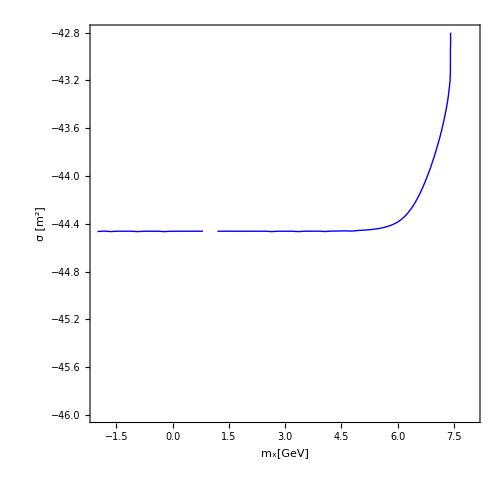

```mathematica
q=ContourPlot[{10^x*CNNboosted[1,10^x,10^y]==2.5*10^31},{x,-2,8},{y,-42.8,-46},Frame->True,RegionFunction->Function[{mdm,xsec},mdm≤ 0.8||mdm ≥ 1.2],FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue}},FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

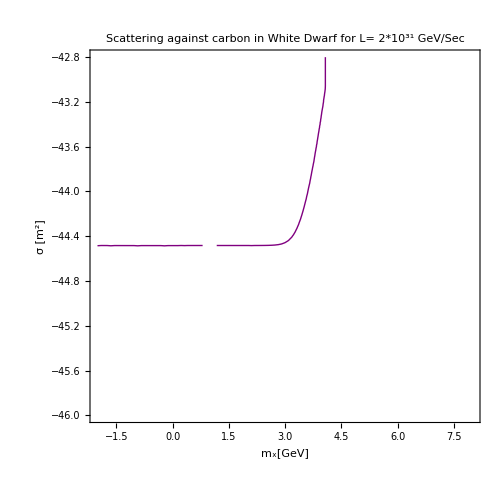

```mathematica
r=ContourPlot[{10^x*a[10^x,10^y]==2.5*10^31},{x,-2,8},{y,-42.8,-46},Frame->True,PlotLabel->"Scattering against carbon in White Dwarf for L= 2*10^31 GeV/Sec ",RegionFunction->Function[{mdm,xsec},mdm≤ 0.8||mdm ≥ 1.2],FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Purple}},FrameLabel->{Style["m_x[GeV]",FontSize->20,Bold],Style["σ [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

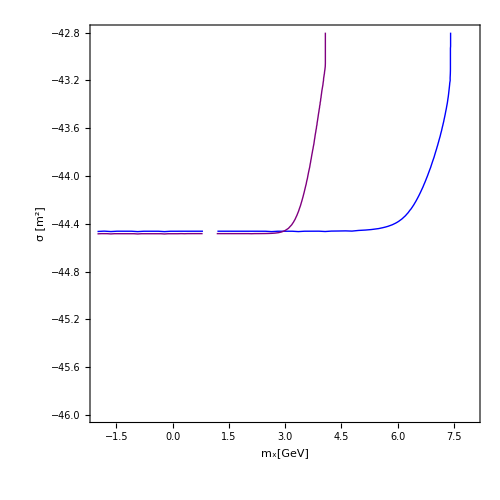

```mathematica
Show[q,r]
```

```mathematica
(*Check*)
```

```mathematica
kb=1.38*10^-23;
T=10^7;
vcarbon=((3*kb*T)/(12*1.78*10^-27))^0.5/1000
```

139.219

```mathematica
vxmax=((3*kb*T)/(10^0*1.78*10^-27))^0.5/1000
```

482.27

```mathematica
vxmin=((3*kb*T)/(10^6*1.78*10^-27))^0.5/1000
```

0.48227

```mathematica
mevapwd=(3*kb*T)/((6*10^6)^2)*5.62*10^26*1000(*in MeV*)
```

6.463

```mathematica
mevapsun=(3*kb*T)/((618*10^3)^2)*5.62*10^26(*in GeV*)
```

0.6092